want to derive the standard deviation for the sampled standard deviation of a distribution

```mathematica
PDF[ChiSquareDistribution[n-1] σ^2 1/(n-1),x]
```

PDF[(σ^2 ChiSquareDistribution[-1+n])/(-1+n),x]

```mathematica
Variance[ChiSquareDistribution[n-1]]
```

2 (-1+n)

```mathematica
distS2=Simplify[PDF[ChiSquareDistribution[n-1],(n-1)S2/σ^2] ,Assumptions->{S2>0,n>0,σ^2>0,σ∈Reals,(n-1)S2/σ^2>0}]
normfac=Integrate[distS2/.S2->x,{x,0,∞},Assumptions->{n>1,σ>0,σ∈Reals,Re[σ^2]>0}]
distS2norm=distS2/normfac
Integrate[distS2norm/.S2->x,{x,0,∞},Assumptions->{n>1,σ>0,σ∈Reals,Re[σ^2]>0}]
assum={n>2,σ>0,σ∈Reals,Re[σ^2]>0};
distS2fun[x_]:=distS2norm/.{S2->x}
Integrate[distS2fun[x],{x,0,∞},Assumptions->assum]
```

(2^(1/2-n/2) ⅇ^(-((-1+n) S2)/(2 σ^2)) (((-1+n) S2)/σ^2)^(1/2 (-3+n)))/Gamma[1/2 (-1+n)]

σ^2/(-1+n)

(2^(1/2-n/2) ⅇ^(-((-1+n) S2)/(2 σ^2)) (-1+n) (((-1+n) S2)/σ^2)^(1/2 (-3+n)))/(σ^2 Gamma[1/2 (-1+n)])

1

1

```mathematica
meanvarS2=Integrate[x distS2fun[x],{x,0,∞},Assumptions->{n>1,σ>0,σ∈Reals,Re[σ^2]>0}]
```

σ^2

```mathematica
varvar=Integrate[(x-meanvarS2)^2 distS2fun[x],{x,0,∞},Assumptions->assum]
```

(2 σ^4)/(-1+n)

```mathematica
SfromS2[S2_]=Sqrt[S2]
S2fromS[S_]=S^2
```

√S2

S^2

```mathematica
distS[S_]=2*S*distS2fun[S2fromS[S]]
```

(2^(3/2-n/2) ⅇ^(-((-1+n) S^2)/(2 σ^2)) (-1+n) S (((-1+n) S^2)/σ^2)^(1/2 (-3+n)))/(σ^2 Gamma[1/2 (-1+n)])

```mathematica
Integrate[distS[x],{x,0,∞},Assumptions->assum]
```

1

```mathematica
meanstd=Integrate[x*distS[x],{x,0,∞},Assumptions->assum]
```

(√2 σ Gamma[n/2])/(√(-1+n) Gamma[1/2 (-1+n)])

```mathematica
c4=√(2/(n-1))Gamma[n/2]/Gamma[(n-1)/2]
```

(√2 √(1/(-1+n)) Gamma[n/2])/Gamma[1/2 (-1+n)]

```mathematica
Simplify[meanstd/c4,Assumptions->assum]
```

σ

```mathematica
varstd=Integrate[(x-meanstd)^2*distS[x],{x,0,∞},Assumptions->assum]
```

σ^2 (1-(2 Gamma[n/2]^2)/((-1+n) Gamma[1/2 (-1+n)]^2))

```mathematica
stdstd=FullSimplify[√varstd,Assumptions->assum]
```

σ √(1-(2 Gamma[n/2]^2)/((-1+n) Gamma[1/2 (-1+n)]^2))

```mathematica
Equal[σ √(1-c4^2),stdstd]
```

True

```mathematica
stdstd=σ √(1-c4^2)
```

σ √(1-(2 Gamma[n/2]^2)/((-1+n) Gamma[1/2 (-1+n)]^2))

If we instead start with the distribution of the estimated variance and propagate the standard deviation in the variance through the 
std from variance formula S=√(S^2) then we get std(std(sample)) =1/2 √(var(var(sample)))

```mathematica
approxstdstd=1/2 √varvar/σ
```

(√(σ^4/(-1+n)))/(√2 σ)

```mathematica
Simplify[approxstdstd,Assumptions->assum]
```

σ/(√2 √(-1+n))

```mathematica
Simplify[approxstdstd/stdstd,Assumptions->assum]
```

1/(√(-2+2 n-(4 Gamma[n/2]^2)/Gamma[1/2 (-1+n)]^2))

```mathematica
N[Simplify[approxstdstd/stdstd,Assumptions->assum]/.{n->10}]
```

1.01492

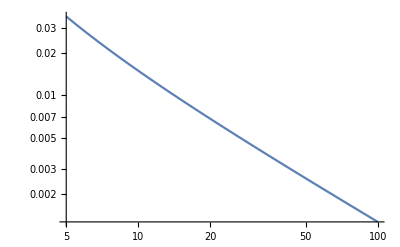

```mathematica
LogLogPlot[Simplify[approxstdstd/stdstd-1,Assumptions->assum]/.{n->x},{x,5,100}]
```

As we can see this gives a tiny difference

sdfsdf

```mathematica
N[c4-1/.n->1000]
```

-0.000250219

```mathematica
N[1-c4/.n->1000]
```

0.000250219